```mathematica
NL=5; (* количество полос разложения *)
Array[KN,NL]; (* массив длин КИХ фильтров нечетной длины *)
KnAll=5; (* зададим все длины КИХ фильтров одинаковыми *)
For[i=1,i<=NL,i++,KN[i]=KnAll];
Array[K,NL]; (* количество положительных коэффициентов КИХ фильтров *)
For[i=1,i<=NL,i++,K[i]=(KN[i]-1)/2];
KMax=K[1];
For[i=1,i<NL,i++,KMax=Max[KMax,K[i+1]]];
(* h[i] - массивы коэффициентов прямых фильтров, начинаются с нулевого индекса *)
For[i=1,i<=NL,i++,Array[h[i],K[i]+1,0]];
(* прореженные характеристики прямых фильтров *)
(* j - индекс прореженной части *)
(* k - индекс фильтра *)
signFunk[i_,k_]:=If[(i>0)&&(Mod[k,2]==0),-1,1];
Do[Do[H[k][j]=
Sum[signFunk[i,k]*h[k][Abs[i]]*x^(i+KMax),{i,-K[k]+j-1,K[k],NL}],{j,1,NL}],{k,1,NL}];

Array[KDet,NL, 0]; (* количество коэффициентов в определителях *)
M0={{H[1][1],H[2][1],H[3][1],H[4][1],H[5][1]},{H[1][2],H[2][2],H[3][2],H[4][2],H[5][2]},
{H[1][3],H[2][3],H[3][3],H[4][3],H[5][3]},{H[1][4],H[2][4],H[3][4],H[4][4],H[5][4]},
{H[1][5],H[2][5],H[3][5],H[4][5],H[5][5]}};
DetM0=Det[M0];
fM0=CoefficientList[DetM0,x];
KDet[0]=Length[fM0];
M1={{1,H[2][1],H[3][1],H[4][1],H[5][1]},{1,H[2][2],H[3][2],H[4][2],H[5][2]},
{1,H[2][3],H[3][3],H[4][3],H[5][3]},{1,H[2][4],H[3][4],H[4][4],H[5][4]},
{1,H[2][5],H[3][5],H[4][5],H[5][5]}};
DetM1=Det[M1];
fM1=CoefficientList[DetM1,x];
KDet[1]=Length[fM1];
M2={{H[1][1],1,H[3][1],H[4][1],H[5][1]},{H[1][2],1,H[3][2],H[4][2],H[5][2]},
{H[1][3],1,H[3][3],H[4][3],H[5][3]},{H[1][4],1,H[3][4],H[4][4],H[5][4]},
{H[1][5],1,H[3][5],H[4][5],H[5][5]}};
DetM2=Det[M2];
fM2=CoefficientList[DetM2,x];
KDet[2]=Length[fM2];
M3={{H[1][1],H[2][1],1,H[4][1],H[5][1]},{H[1][2],H[2][2],1,H[4][2],H[5][2]},
{H[1][3],H[2][3],1,H[4][3],H[5][3]},{H[1][4],H[2][4],1,H[4][4],H[5][4]},
{H[1][5],H[2][5],1,H[4][5],H[5][5]}};
DetM3=Det[M3];
fM3=CoefficientList[DetM3,x];
KDet[3]=Length[fM3];
M4={{H[1][1],H[2][1],H[3][1],1,H[5][1]},{H[1][2],H[2][2],H[3][2],1,H[5][2]},
{H[1][3],H[2][3],H[3][3],1,H[5][3]},{H[1][4],H[2][4],H[3][4],1,H[5][4]},
{H[1][5],H[2][5],H[3][5],1,H[5][5]}};
DetM4=Det[M4];
fM4=CoefficientList[DetM4,x];
KDet[4]=Length[fM4];
M5={{H[1][1],H[2][1],H[3][1],H[4][1],1},{H[1][2],H[2][2],H[3][2],H[4][2],1},
{H[1][3],H[2][3],H[3][3],H[4][3],1},{H[1][4],H[2][4],H[3][4],H[4][4],1},
{H[1][5],H[2][5],H[3][5],H[4][5],1}};
DetM5=Det[M5];
fM5=CoefficientList[DetM5,x];
KDet[5]=Length[fM5];

Array[K1,NL]; (* количество положительных коэффициентов обратных КИХ фильтров *)
For[i=1,i<=NL,i++,K1[i]=(KDet[i]-NL-2)/2];
(* kh[i] - массивы коэффициентов обратных фильтров, начинаются с нулевого индекса *)
For[i=1,i<=NL,i++,Array[kh[i],K1[i]+1,0]];
For[k=1,k≤NL,k++,For[i=K1[k]+1;j=KDet[k],i>0,i--;j--,
kh[k][i-1]=Switch[k,1,fM1[[j]],2,fM2[[j]],3,fM3[[j]],4,fM4[[j]],5,fM5[[j]]]]];

Print["K  : (",K[1],", ",K[2],", ",K[3],", ",K[4],", ",K[5],")  (",
2*K[1]+1,", ", 2*K[2]+1,", ",2*K[3]+1,", ",2*K[4]+1,", ",2*K[5]+1,")"];
Print["K1 : (",K1[1],", ",K1[2],", ",K1[3],", ",K1[4],", ",K1[5],")  (",
2*K1[1]+1,", ", 2*K1[2]+1,", ",2*K1[3]+1,", ",2*K1[4]+1,", ",2*K1[5]+1,")"];
Print["Длина детерминанта - ",KDet[0]];
Print["Середина детерминанта, равная 1, - ",(KDet[0]-2*NL-1)/2];
Print["Количество уравнений - ",K[1]+K[2]+K[3]+K[4]+K[5]+NL];
```

K  : (2, 2, 2, 2, 2)  (5, 5, 5, 5, 5)

K1 : (2, 2, 2, 2, 2)  (5, 5, 5, 5, 5)

Длина детерминанта - 11

Середина детерминанта, равная 1, - 0

Количество уравнений - 15

```mathematica
s=1;
NSlv=NSolve[{
(*fM0[[KDet[0]]]==0,*)
(*fM0[[KDet[0]-NL]]==0,*)
(*fM0[[KDet[0]-2*NL]]==1,*)

Sum[h[1][Abs[i]],{i,-K[1],K[1]}]==s,
Sum[h[1][Abs[i]]*(-1)^i,{i,-K[1],K[1]}]==0,
(*Sum[i^2*h[1][i],{i,1,K[1]}]==0,*)
Sum[i^2*h[1][i]*(-1)^(i-1),{i,1,K[1]}]==0,
(*Sum[i^4*h[1][i],{i,1,K[1]}]==0,*)
(*Sum[i^4*kh[1][i]*(-1)^(i-1),{i,1,K1[1]}]==3.5,*)

Sum[h[2][i]*Sin[Pi*i*0.35],{i,1,K[2]}]==s/2,
Sum[i*h[2][i]*Cos[Pi*i*0.35],{i,1,K[2]}]==0,
(*Sum[i*h[2][i],{i,1,K[2]}]==0,*)
(*Sum[i*h[2][i]*(-1)^(i-1),{i,1,K[2]}]==0,*)
(*Sum[i^3*h[2][i]*(-1)^(i-1),{i,1,K[2]}]==0,
Sum[i^3*h[2][i],{i,1,K[2]}]==0,*)

Sum[h[3][Abs[i]],{i,-K[3],K[3]}]==0,
Sum[h[3][Abs[i]]*(-1)^i,{i,-K[3],K[3]}]==0,
Sum[h[3][Abs[i]]*Cos[Pi*i*0.5],{i,-K[3],K[3]}]==s,
(*Sum[i*h[3][i]*Sin[Pi*i*0.5],{i,1,K[3]}]==0,*)
(*Sum[i^2*h[3][i]*(-1)^(i-1),{i,1,K[3]}]==0,*)
(*Sum[i^2*h[3][i],{i,1,K[3]}]==0,*)
(*Sum[i*h[3][i],{i,1,K[3]}]==0,*)

Sum[h[4][i]*Sin[Pi*i*0.65],{i,1,K[4]}]==s/2,
Sum[i*h[4][i]*Cos[Pi*i*0.65],{i,1,K[4]}]==0,
(*Sum[i*h[4][i],{i,1,K[4]}]==0,*)
(*Sum[i*h[4][i]*(-1)^(i-1),{i,1,K[4]}]==0,*)
(*Sum[i^3*h[4][i],{i,1,K[4]}]==0,
Sum[i^3*h[4][i]*(-1)^(i-1),{i,1,K[4]}]==0,*)

Sum[h[5][Abs[i]],{i,-K[5],K[5]}]==0,
Sum[h[5][Abs[i]]*(-1)^i,{i,-K[5],K[5]}]==s,
Sum[i^2*h[5][i],{i,1,K[5]}]==0,
(*Sum[i^2*h[5][i]*(-1)^(i-1),{i,1,K[5]}]==0,*)
(*Sum[i^4*h[5][i],{i,1,K[5]}]==0,*)
(*Sum[i^4*h[5][i]*(-1)^(i-1),{i,1,K[5]}]==0,*)

h[2][0]==0,
h[4][0]==0
}];
Print["Количество решений - ",Length[NSlv]]
```

Количество решений - 1

Номер решения - 1

Значение детерминанта  = 0.0333319

Корреляция LF-HF   = 0.2

Корреляция LF-MF   = -0.512989

Корреляция MF-HF   = -0.512989

Корреляция MFl-MFh = -0.740431

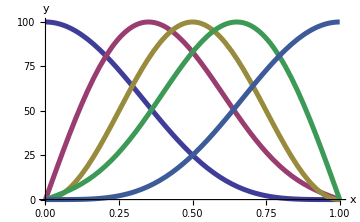
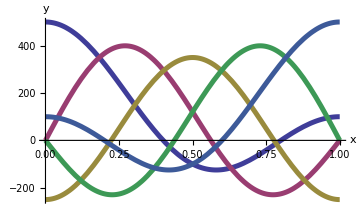

```mathematica
Do[ph[j]=100*(h[j][0]+2*Sum[h[j][i]*Switch[j,1,Cos[Pi*i*x],2,Sin[Pi*i*x],3,Cos[Pi*i*x],4,Sin[Pi*i*x],5,Cos[Pi*i*x]],{i,1,K[1]}]),{j,1,NL}];
Do[pkh[j]=100*(kh[j][0]+2*Sum[kh[j][i]*Switch[j,1,Cos[Pi*i*x],2,Sin[Pi*i*x],3,Cos[Pi*i*x],4,Sin[Pi*i*x],5,Cos[Pi*i*x]],{i,1,K1[1]}])/fM0[[KDet[0]-((KDet[0]-2*NL-1)/2)]],{j,1,NL}];
Do[pkhh[i]=ph[i]*pkh[i]/(500*fM0[[KDet[0]-((KDet[0]-2*NL-1)/2)]]),{i,1,NL}];

Do[Print["Номер решения - ",kk];
Print["Значение детерминанта  = ",fM0[[KDet[0]-((KDet[0]-2*NL-1)/2)]]/.NSlv[[kk]]];
Array[Sq,NL];
Do[Sq[j]=Sqrt[Sum[(kh[j][Abs[i]]/.NSlv[[kk]])^2,{i,-K1[j],K1[j]}]],{j,1,NL}];
lfhf=Sum[(kh[1][Abs[i]]/.NSlv[[kk]])*(kh[5][Abs[i]]/.NSlv[[kk]]),{i,-Min[K1[1],K1[5]],Min[K1[1],K1[5]]}]/(Sq[1]*Sq[5]);
Print["Корреляция LF-HF   = ",lfhf];
lfmf=Sum[(kh[1][Abs[i]]/.NSlv[[kk]])*(kh[3][Abs[i]]/.NSlv[[kk]]),{i,-Min[K1[1],K1[3]],Min[K1[1],K1[3]]}]/(Sq[1]*Sq[3]);
Print["Корреляция LF-MF   = ",lfmf];
mfhf=Sum[(kh[5][Abs[i]]/.NSlv[[kk]])*(kh[3][Abs[i]]/.NSlv[[kk]]),{i,-Min[K1[5],K1[3]],Min[K1[5],K1[3]]}]/(Sq[5]*Sq[3]);
Print["Корреляция MF-HF   = ",mfhf];
mflmfh=Sum[(kh[2][Abs[i]]/.NSlv[[kk]])*(kh[4][Abs[i]]/.NSlv[[kk]]),{i,-Min[K1[2],K1[4]],Min[K1[2],K1[4]]}]/(Sq[2]*Sq[4]);
Print["Корреляция MFl-MFh = ",mflmfh];
(*Do[Print[ssh[j]=Sqrt[Sum[(h[j][Abs[i]]/.NSlv[[kk]])^2,{i,-K[j],K[j]}]]],{j,1,NL}];*)
(*Print[((h[1][0]/.NSLv[[kk]])*(g[0]/.NSLv[[kk]])+2*(h[1]/.NSLv[[kk]])*(g[1]/.NSLv[[kk]]))/(ssh*ssg)];*)
(*Do[Print[Sum[(h[j][i]/.NSlv[[kk]])^2,{i,2,K[j]}]/((h[j][0]/.NSlv[[kk]])^2+2*Sum[(h[j][i]/.NSlv[[kk]])^2,{i,2,K[j]}])],{j,1,NL}];*)
Print[Plot[{ph[1]/.NSlv[[kk]],ph[2]/.NSlv[[kk]],ph[3]/.NSlv[[kk]],ph[4]/.NSlv[[kk]],ph[5]/.NSlv[[kk]]},{x,0,1},AxesLabel->{"x","y"},
LabelStyle->Directive[FontFamily->"Times",FontSize->12],PlotStyle->{Thickness[0.01]},ImageSize->Medium],Plot[{pkh[1]/.NSlv[[kk]],pkh[2]/.NSlv[[kk]],pkh[3]/.NSlv[[kk]],pkh[4]/.NSlv[[kk]],pkh[5]/.NSlv[[kk]]},{x,0,1},AxesLabel->{"x","y"},
LabelStyle->Directive[FontFamily->"Times",FontSize->12],PlotStyle->{Thickness[0.01]},ImageSize->Medium]],{kk,Length[NSlv]}]

(*kk=1;
Plot[{ph[1]/.NSlv[[kk]],ph[2]/.NSlv[[kk]],ph[3]/.NSlv[[kk]],ph[4]/.NSlv[[kk]],ph[5]/.NSlv[[kk]]},{x,0,1},AxesLabel->{"x","y"},
LabelStyle->Directive[FontFamily->"Times",FontSize->12],PlotStyle->{Thickness[0.01]}]
Plot[{pkh[1]/.NSlv[[kk]],pkh[2]/.NSlv[[kk]],pkh[3]/.NSlv[[kk]],pkh[4]/.NSlv[[kk]],pkh[5]/.NSlv[[kk]]},{x,0,1},AxesLabel->{"x","y"},
LabelStyle->Directive[FontFamily->"Times",FontSize->12],PlotStyle->{Thickness[0.01]}]*)
(*Plot[{pkhh[1]/.NSlv[[kk]],pkhh[2]/.NSlv[[kk]],pkhh[3]/.NSlv[[kk]],pkhh[4]/.NSlv[[kk]],pkhh[5]/.NSlv[[kk]],(pkhh[1]+pkhh[2]+pkhh[3]+pkhh[4]+pkhh[5])/.NSlv[[kk]]},{x,0,1},AxesLabel->{"x","y"},
LabelStyle->Directive[FontFamily->"Times",FontSize->12],PlotStyle->{Thickness[0.01]}]*)
```

0.139754	0.447214	0.379002	-0.659627	-0.544862	-0.688247	-0.379002	0.659627	0.139754	0.447214

0.559017	0.447214	0.981394	-0.25474	0.	0.	0.981394	-0.25474	-0.559017	-0.447214

0.838525	0.447214	0.	0.	1.08972	0.229416	0.	0.	0.838525	0.447214

0.559017	0.447214	-0.981394	0.25474	0.	0.	-0.981394	0.25474	-0.559017	-0.447214

0.139754	0.447214	-0.379002	0.659627	-0.544862	-0.688247	0.379002	-0.659627	0.139754	0.447214

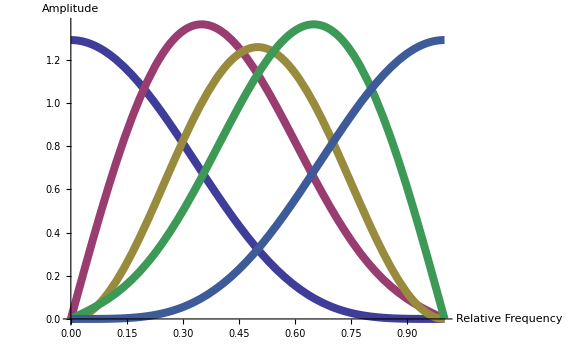

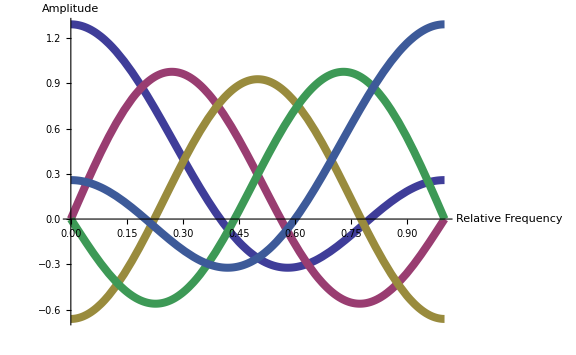

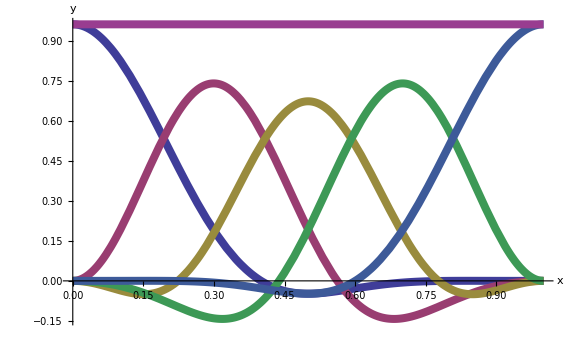

```mathematica
kk=1;(* 0.05 - 20 28 33 *) (* 0.01 - 25 *) (* 0 - 12 13 *) (* 0.03 - 24 27 28 *) (* 0.07 - 20 26 27 *) (* 0.1 - 20 29 30 31 34 *)
KMax2=Max[K[1],K1[1]];
For[i=1,i<NL,i++,KMax2=Max[KMax2,K[i+1],K1[i+1]]];
min=10^-12;

Do[
Array[h2[j],2*KMax2+1,-KMax2];
For[i=-KMax2,i≤KMax2,i++,h2[j][i]=0.0];
For[i=-K[j],i≤K[j],i++,h2[j][i]=h[j][Abs[i]]/.NSlv[[kk]]];
Array[kh2[j],2*KMax2+1,-KMax2];
For[i=-KMax2,i≤KMax2,i++,kh2[j][i]=0.0];
For[i=-K1[j],i≤K1[j],i++,kh2[j][i]=(kh[j][Abs[i]]/fM0[[KDet[0]-((KDet[0]-2*NL-1)/2)]])/.NSlv[[kk]]];
shh[j]=Sqrt[Sum[h2[j][i]^2,{i,-K[j],K[j]}]];
skh[j]=Sqrt[Sum[kh2[j][i]^2,{i,-K1[j],K1[j]}]],
{j,1,NL,2}];
Do[
Array[h2[j],2*KMax2+1,-KMax2];
For[i=-KMax2,i≤KMax2,i++,h2[j][i]=0.0];
For[i=-K[j],i≤K[j],i++,h2[j][i]=-Sign[i]*h[j][Abs[i]]/.NSlv[[kk]]];
Array[kh2[j],2*KMax2+1,-KMax2];
For[i=-KMax2,i≤KMax2,i++,kh2[j][i]=0.0];
For[i=-K1[j],i≤K1[j],i++,kh2[j][i]=(Sign[i]*kh[j][Abs[i]]/fM0[[KDet[0]-((KDet[0]-2*NL-1)/2)]])/.NSlv[[kk]]];
shh[j]=Sqrt[Sum[h2[j][i]^2,{i,-K[j],K[j]}]];
skh[j]=Sqrt[Sum[kh2[j][i]^2,{i,-K1[j],K1[j]}]],
{j,2,NL,2}];

(* нормировка по обратным функциям *)
Do[
For[i=-K[j],i≤K[j],i++,h2[j][i]=h2[j][i]*skh[j]];
For[i=-K1[j],i≤K1[j],i++,kh2[j][i]=kh2[j][i]/skh[j]],
{j,1,NL}];

(* нормировка по прямым функциям *)
(*Do[
For[i=-K[j],i≤K[j],i++,h2[j][i]=h2[j][i]/shh[j]];
For[i=-K1[j],i≤K1[j],i++,kh2[j][i]=kh2[j][i]*shh[j]],
{j,1,NL}];*)

(* ограничение *)
Do[
For[i=-K[j],i≤K[j],i++,ss=h2[j][i];h2[j][i]=If[Abs[ss]<min,0.0,ss]];
For[i=-K1[j],i≤K1[j],i++,ss=kh2[j][i];kh2[j][i]=If[Abs[ss]<min,0.0,ss]],
{j,1,NL}];

sep="\t";
For[i=-KMax2,i≤KMax2,i++,Print[h2[1][i],sep,kh2[1][i],sep,h2[2][i],sep,kh2[2][i],sep,h2[3][i],sep,kh2[3][i],sep,h2[4][i],sep,kh2[4][i],sep,h2[5][i],sep,kh2[5][i]]];


ampl=1.0/Sqrt[3];
Do[
ph2[j]=ampl*(h2[j][0]+2*Sum[h2[j][i]*Switch[j,1,Cos[Pi*i*x],2,-Sin[Pi*i*x],3,Cos[Pi*i*x],4,-Sin[Pi*i*x],5,Cos[Pi*i*x]],{i,1,KMax2}]);
pkh2[j]=ampl*(kh2[j][0]+2*Sum[kh2[j][i]*Switch[j,1,Cos[Pi*i*x],2,Sin[Pi*i*x],3,Cos[Pi*i*x],4,Sin[Pi*i*x],5,Cos[Pi*i*x]],{i,1,KMax2}]);
pkhh2[j]=ph2[j]*pkh2[j]/(ampl*3),
{j,1,NL}];

Needs["PlotLegends`"];

(*Print[h2[0]*g2[0]+2*h2[1]*g2[1]];
Print[kh2[0]*kg2[0]+2*kh2[1]*kg2[1]];*)
Plot[{ph2[1],ph2[2],ph2[3],ph2[4],ph2[5]},{x,0,1},AxesLabel->{"Relative Frequency","Amplitude"},PlotLegend->{"LF","MFl","MF","MFh","HF"},
LabelStyle->Directive[FontFamily->"Times",FontSize->14],PlotStyle->{Thickness[0.01]},AxesStyle->Thick,ImageSize->Large,LegendPosition->{0.6,-0.1},LegendSize->0.5,LegendShadow->None]
(*plot2=Plot[{Abs[ph2[1]],Abs[ph2[2]],Abs[ph2[3]],Abs[ph2[4]],Abs[ph2[5]]},{x,0,1},AxesLabel->{"Relative Frequency","Amplitude"},PlotLegend->{"LF","MFl","MF","MFh","HF"},
LabelStyle->Directive[FontFamily->"Times",FontSize->14],PlotStyle->{Thickness[0.01]},AxesStyle->Thick,ImageSize->Large,LegendPosition->{0.4,-0.3},LegendSize->0.5,LegendShadow->None]
Export["d:\plot2.eps",plot2]*)
Plot[{pkh2[1],pkh2[2],pkh2[3],pkh2[4],pkh2[5]},{x,0,1},AxesLabel->{"Relative Frequency","Amplitude"},PlotLegend->{"LF","MFl","MF","MFh","HF"},
LabelStyle->Directive[FontFamily->"Times",FontSize->14],PlotStyle->{Thickness[0.01]},AxesStyle->Thick,ImageSize->Large,LegendPosition->{0.6,-0.1},LegendSize->0.5,LegendShadow->None]
(*plot1=Plot[{Abs[pkh2[1]],Abs[pkh2[2]],Abs[pkh2[3]],Abs[pkh2[4]],Abs[pkh2[5]]},{x,0,1},AxesLabel->{"Relative Frequency","Amplitude"},PlotLegend->{"LF","MFl","MF","MFh","HF"},
LabelStyle->Directive[FontFamily->"Times",FontSize->14],PlotStyle->{Thickness[0.01]},AxesStyle->Thick,ImageSize->Large,LegendPosition->{0.4,-0.3},LegendSize->0.5,LegendShadow->None]
Export["d:\plot1.eps",plot1]*)
Plot[{pkhh2[1],pkhh2[2],pkhh2[3],pkhh2[4],pkhh2[5],(pkhh2[1]+pkhh2[2]+pkhh2[3]+pkhh2[4]+pkhh2[5])},{x,0,1},AxesLabel->{"x","y"},
LabelStyle->Directive[FontFamily->"Times",FontSize->12],PlotStyle->{Thickness[0.01]}]
```